```mathematica
x4p= Import["/Users/ashutosh/LCX_analysis/FNO/X1_4_X1_Mu_X_0.077"];
```

```mathematica
MatrixPlot[%257,PlotTheme->"Detailed"]
```

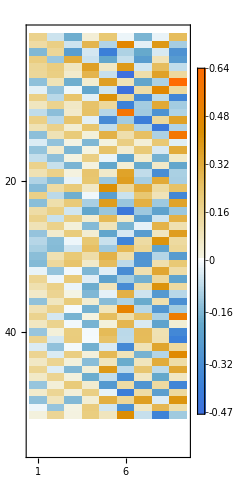

```mathematica
x19p= Import["/Users/ashutosh/LCX_analysis/FNO/X1_19_X1_Mu_X_0.077"];
```

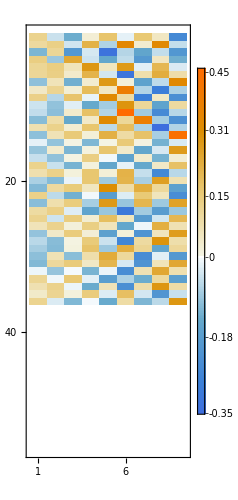

```mathematica
MatrixPlot[%260,PlotTheme->"Detailed"]
```

```mathematica
muxguess= Import["/Users/ashutosh/LCX_analysis/FNO/Mu_Xguess"];
```

```mathematica
x0p= Import["/Users/ashutosh/LCX_analysis/FNO/X1_0_X1_Mu_X_0.077"];
```

```mathematica
MatrixPlot[%263,PlotTheme->"Detailed"]
```

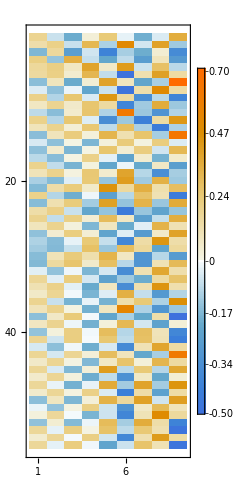

```mathematica
filt[i_,j_]:=If[Abs[ x0p[[i,j]]] > 0.05 ,x0p [[i,j]],0];
```

```mathematica
x0pp = Table[filt[i,j],{i,55},{j,9}];
```

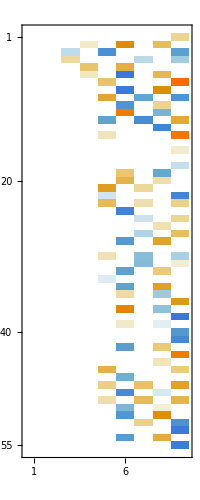

```mathematica
MatrixPlot[%677]
```

```mathematica
x4pcan= Import["/Users/ashutosh/LCX_analysis/can/X1_4_X1_Mu_X_0.077"];
```

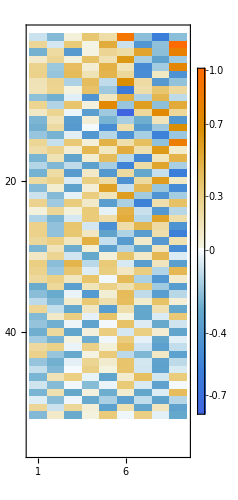

```mathematica
MatrixPlot[%271,PlotTheme->"Detailed"]
```

```mathematica
x19pcan= Import["/Users/ashutosh/LCX_analysis/can/X1_19_X1_Mu_X_0.077"];
```

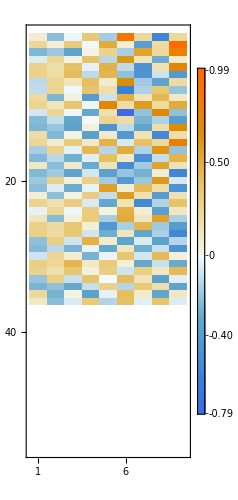

```mathematica
MatrixPlot[%274,PlotTheme->"Detailed"]
```

```mathematica
x0pcan= Import["/Users/ashutosh/LCX_analysis/can/X1_0_X1_Mu_X_0.077"];
```

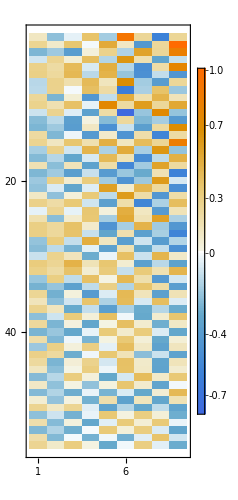

```mathematica
MatrixPlot[%268,PlotTheme->"Detailed"]
```

```mathematica
remove T1 and T2 in can and NO basis and see how magnitudes of T1 and T2 change with the truncation
repeat the same with X1 and X2
besure of the pattern-then try to explain things based on the mathematics-focus on the amplitude
equation constraints,think why the given pattern,what is it an artifact of..
compare the residuals of T1 and T2 values after truncation- think of what is missing and how should the 
remaining T1 and T2s respond to satisfy the amplitude equations. repeat the same with X1 and X2
```

```mathematica
MUFNO = Import["/Users/ashutosh/mathematica_data/fno/MU_X_IA_FNO"];
```

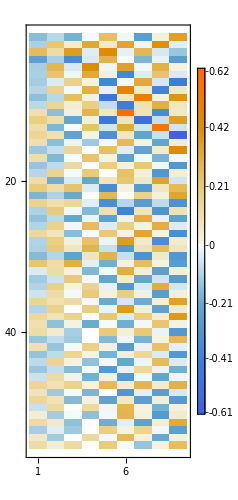

```mathematica
MatrixPlot[%688,PlotTheme->"Detailed"]
```

```mathematica
MUXCAN = Import["/Users/ashutosh/mathematica_data/fno/MU_X_IA_CAN","Table"] ;
```

```mathematica
filtcan[i_,j_]:=If[Abs[ MUXCAN[[i,j]]] > 0.05 ,MUXCAN [[i,j]],0];
```

```mathematica
MUXCANF = Table[filtcan[i,j],{i,55},{j,9}];
```

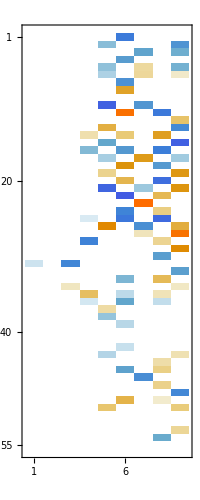

```mathematica
MatrixPlot[%722]
```

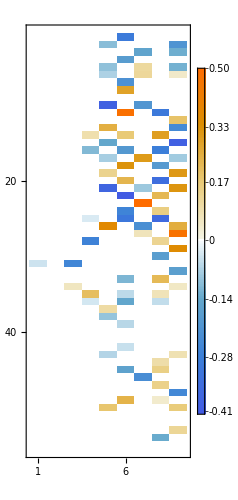

```mathematica
MatrixPlot[%722,PlotTheme->"Detailed"]
```

```mathematica
filtfno[i_,j_]:=If[Abs[ MUFNO[[i,j]]] > 0.05 ,MUFNO [[i,j]],0];
```

```mathematica
MUXFNOF = Table[filtfno[i,j],{i,55},{j,9}];
```

```mathematica
MatrixPlot[%708,PlotTheme->"Detailed"]
```

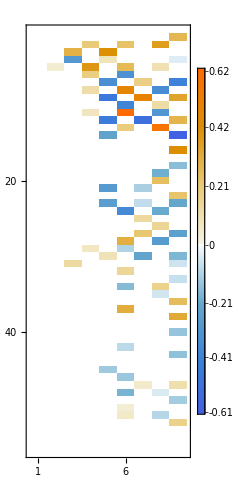
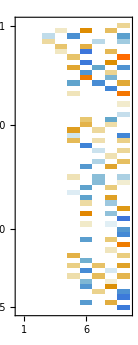
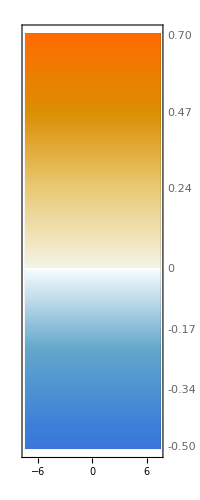
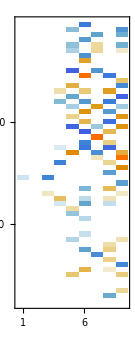
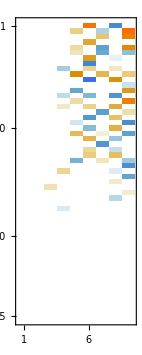

```mathematica
X0pfno =  Import["/Users/ashutosh/LCX_analysis/FNO/X1_0_X1_Mu_X_0.077"];
```

```mathematica
filtfno1[i_,j_]:=If[Abs[ X0pfno[[i,j]]] > 0.05 ,X0pfno [[i,j]],0];
```

```mathematica
X0pfno  = Table[filtfno1[i,j],{i,55},{j,9}];
```

```mathematica
MatrixPlot[%714]
```

-Graphics-

```mathematica
filtcan1[i_,j_]:=If[Abs[ x0pcan[[i,j]]] > 0.05 ,x0pcan [[i,j]],0];
```

```mathematica
X0pcan  = Table[filtcan1[i,j],{i,55},{j,9}];
```

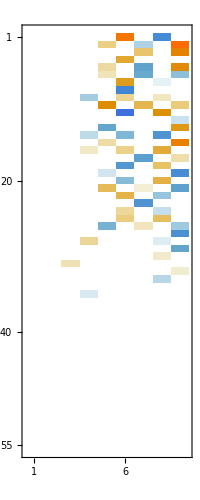

```mathematica
MatrixPlot[%719]
```